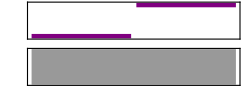

```mathematica
Sound[{SoundNote["C7"],SoundNote["G7"]}]
```

```mathematica
Sound[{Play[Sin[1000t(1+t^2)],{t,0,.2}],Play[Sin[500t (1+t^3)],{t,0,.5}]}]
```

-Graphics-

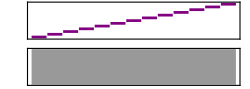

```mathematica
Sound[Table[SoundNote[i],{i,0,12}]]
```

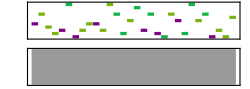

```mathematica
Sound[SoundNote[#,1,RandomChoice[{"Piano","Cello","Tuba"}]]& /@ RandomInteger[12, 30], 4]
```

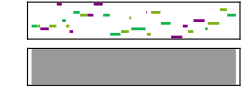

```mathematica
Sound[SoundNote[#,RandomReal[2],RandomChoice[{"Piano","Cello","Tuba"}]]& /@ RandomInteger[12, 30], 4]
```

```mathematica
Play[Sin[2Pi 440 t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sin[700 t+25 t Sin[350 t]],{t,0,4}]
```

-Graphics-

```mathematica
ListPlay[RandomReal[{-1,1},8000]]
```

-Graphics-

```mathematica
Sound[SampledSoundList[Table[Sin[2π 500 t],{t,0,1,1./2000}],2000]]
```

-Graphics-

```mathematica
Play[(2+Cos[20 t]) * Sin[3000 t + 2 Sin[50 t] ],{t,0,2}]
```

-Graphics-